## Tupik_D_L

## Lab_work_5: Численные расчёты в системе Mathematica

## Задание 1

### a. Пробел выполняет роль знака умножения

```mathematica
7 8
```

56

### б. Введение дополнительных пробелом не изменяют результата вычислений

```mathematica
7              8
```

56

### в. Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.

```mathematica
3^(1/2)
```

√3

```mathematica
1/2
```

1/2

### г. Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды.

```mathematica
3.^(1/2)
```

1.73205

```mathematica
1./2
```

0.5

### д. Для изменения стандартного порядка выполнения операций используются круглые скобки

```mathematica
3*(1+2)
```

9

```mathematica
3*1+2
```

5

## Задание 2

### а. С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Проверить точность полученного результата с помощью функции Precision

```mathematica
x = N[Sqrt[17], 200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[x]
```

200.

### б. Найти приближенное значение числа e^(Pi *Sqrt[163]) с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа. Для стандартного округления чисел используется функция Round.

```mathematica
y = N[E^(Pi *Sqrt[163]), 40]
```

2.625374126407687439999999999992500725972×10^17

```mathematica
Round[y]
```

262537412640768744

### в. Вычислите

```mathematica
(10*(10.8*(10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
10^(-24) * 10^12/10^(-14)*(32768/2^9)^(1/2)
```

800

### г. Последовательно введите выражения

```mathematica
5>3
```

True

```mathematica
5<2
```

False

```mathematica
Pi^E > E^Pi
```

False

```mathematica
N[Pi^E]
```

22.4592

```mathematica
N[E^Pi]
```

23.1407

## Задание 3

### а. Решить уравнения:

```mathematica
Clear[x];
```

```mathematica
NSolve[(x+2)^(1/2)+4  x == 4, x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3*x^2+5==0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

### б. Решить системы уравнений:

```mathematica
Clear[x, y];
```

```mathematica
NSolve[{x^2+x*y+y^2 == 1, x^3 + x^2*y + x * y^2 + y^3 == 4}, {x, y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3*z == 34, x+y-z==-1, -x + 2*y + 3*z == 4}, {x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

### в. Придумайте уравнение или систему полиномиальных уравнений и найдите её численное решение

```mathematica
Clear[x, y];
```

```mathematica
NSolve[{(x^2 + 4*y^2)/(x*y) == 5, 2*x^2 - y^2 == 31}, {x, y}]
```

{{x→4.,y→1.},{x→-4.,y→-1.},{x→5.56776,y→5.56776},{x→-5.56776,y→-5.56776}}

## Задание 4

### Используя функцию FindRoot, найдите решение следующего уравнения (Вариант №21):

```mathematica
Clear[x, y];
```

```mathematica
FindRoot[2*x^4-3*x^3+4*x-1==Tanh[x], {x, -2, 1}]
```

{x→0.364997}

## Задание 5

### Найдите решение одного из следующих дифференциальных уравнений на заданном отрезке (Вариант №21):

```mathematica
Remove[x, y];
```

```mathematica
solve = NDSolve[{y''[x]-4*x*y'[x]+(4*x^2+3*x+4)*y[x]==0, y[0]==-10, y'[0]==-5},y ,{x, -1, 2}]
```

{{y→InterpolatingFunction[…]}}

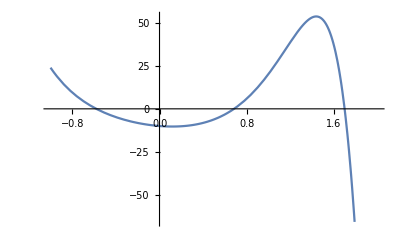

```mathematica
Plot[y[x]/.solve, {x,-1, 2}]
```

### Используя найденное решение:

#### а. Найдите на заданном отрезке корни уравнения y(x) = 0

```mathematica
solveA1=FindRoot[(y[x]/.solve)==0, {x,-0.6}]
```

{x→-0.579889}

```mathematica
solveA2=FindRoot[(y[x]/.solve)==0, {x,0.6}]
```

{x→0.683748}

```mathematica
solveA3=FindRoot[(y[x]/.solve)==0, {x,1.7}]
```

{x→1.69854}

#### б. Найдите значения производной y’(x) в точках, где y(x) = 0

```mathematica
D[y[x]/.solve,x]/.solveA1
```

{-32.7845}

```mathematica
D[y[x]/.solve,x]/.solveA2
```

{43.5748}

```mathematica
D[y[x]/.solve,x]/.solveA3
```

{-529.231}

#### в. Выберите одну из точек, в которых производная функции y(x)=0, и вычислите значение функции в этой точке

```mathematica
solveV1 = FindRoot[D[y[x]/.solve,x]==0, {x,0.2}]
```

{x→0.117935}

```mathematica
y[x]/.solve/.solveV1
```

{-10.3011}

#### г. C помощью функции FindMinimum найдите точки, в которых функция y(x) имеет локальный минимум или максимум, и сравните полученные результаты со значениями, найденными в пункте (в)

```mathematica
FindMinimum[y[x]/.solve, {x, 0.2}]
```

{-10.3011,{x→0.117935}}

## Задание 6

```mathematica
Remove[x, y];
```

### а. Задайте произвольные численные значения параметров а, b, c, d, e в зависимостях и используя функцию Table, определите список численных данных, каждый элемент которого содержит 2 соответствующих элемента (x, y). Область изменения x и шаг выбрать самостоятельно. С помощью функции Random внести в каждой точке x случайное перемещение y (первые 2)

```mathematica
a = 10;
b = 20;
c = 30;
d = 40;
e = 50;
```

```mathematica
y1[x_] := a + b*x + c*x^2+d*x^3+e*x^4
y2[x_] := a + b*x + c* Sin[x] + d*Cos[x]
```

```mathematica
task1Y1 = Table[{x,y1[x](1+Random[Real, {-0.1,0.1}])}, {x,0,2,0.1}]
```

{{0.,9.10553},{0.1,12.7632},{0.2,14.1726},{0.3,21.6567},{0.4,24.513},{0.5,36.0203},{0.6,52.4681},{0.7,59.2342},{0.8,78.3992},{0.9,117.025},{1.,149.693},{1.1,177.016},{1.2,270.472},{1.3,297.518},{1.4,390.893},{1.5,520.228},{1.6,570.215},{1.7,815.468},{1.8,874.446},{1.9,1032.42},{2.,1327.7}}

```mathematica
task1Y2 = Table[{x,y2[x](1+Random[Real, {-0.1,0.1}])}, {x,0,2,0.1}]
```

{{0.,51.7993},{0.1,59.1753},{0.2,61.6603},{0.3,60.5152},{0.4,61.2044},{0.5,63.6914},{0.6,71.8139},{0.7,72.722},{0.8,74.3771},{0.9,79.3458},{1.,83.9321},{1.1,74.5456},{1.2,76.1733},{1.3,82.8499},{1.4,75.0367},{1.5,76.0912},{1.6,74.9121},{1.7,63.8313},{1.8,69.9936},{1.9,69.6115},{2.,54.8651}}

### б. Изобразить полученные точки на координатной плоскости

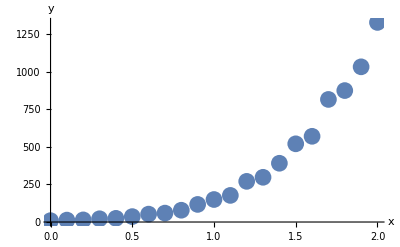

```mathematica
taskPlot1=ListPlot[task1Y1, PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
```

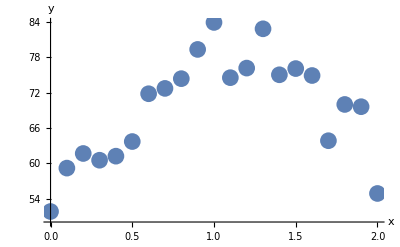

```mathematica
taskPlot2=ListPlot[task1Y2, PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
```

### в. С помощью функции Fit, найдите наилучшую кривую, аппроксимирующую численные данные

```mathematica
task2Y1 = Fit[task1Y1, {1,x,x^2, x^3, x^4},x]
```

11.0047+2.70028 x+71.142 x^2+3.58054 x^3+60.3867 x^4

```mathematica
task2Y2 = Fit[task1Y2, {1, x, Cos[x], Sin[x]}, x]
```

73.089-43.1493 x-19.6655 Cos[x]+69.4194 Sin[x]

### г. На одной координатной плоскости изобразите найденную кривую вместе с экспериментальными точками

```mathematica
taskFitPlot1 = Plot[task2Y1, {x, 0, 2}]
```

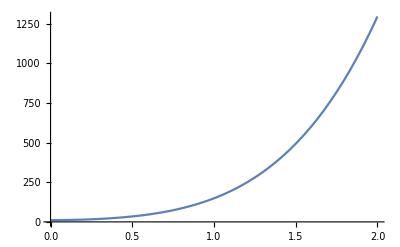

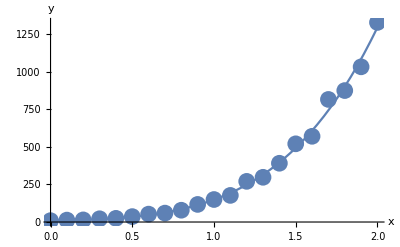

```mathematica
Show[taskPlot1, taskFitPlot1]
```

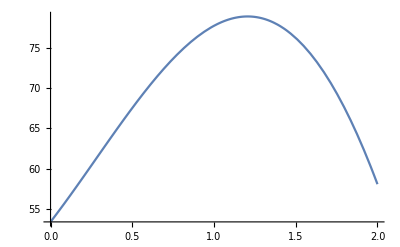

```mathematica
taskFitPlot2 = Plot[task2Y2, {x, 0, 2}]
```

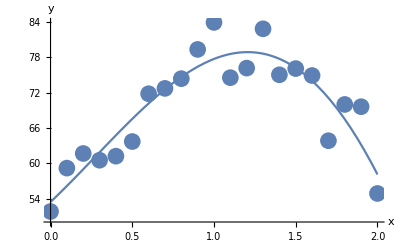

```mathematica
Show[taskPlot2, taskFitPlot2]
```